15.6269

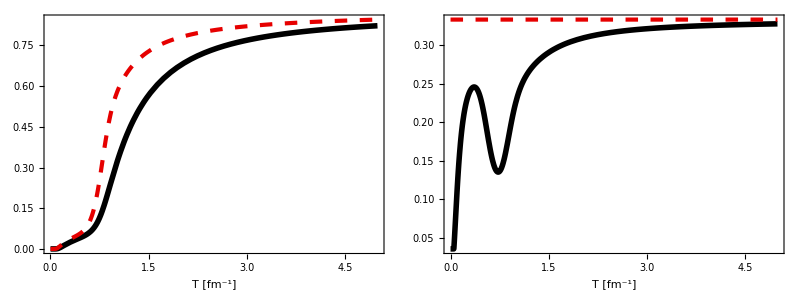

```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

styles={Directive[RGBColor[0,0,0],AbsoluteThickness[4]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0.5],AbsoluteThickness[2],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[2],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[2],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};

FrameTicksFontSize=20;
FrameFontSize=20;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->0.75,ImageSize->Medium,PlotStyle->styles,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];

rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->10000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];


eosDataRaw=Import[wd<>"/eos.dat"];
eosData= Take[eosDataRaw,{3,Length[eosDataRaw]}];

(* Subscript[ϵ, eq](T) *)
LogEDLogTInt = Interpolation[eosData[[All,{1,2}]]];
edInt[T_] = 10^LogEDLogTInt[Log[10,T]];

(* Subscript[P, eq](T) *)
LogPLogTInt = Interpolation[eosData[[All,{1,4}]]];
PInt[T_] = 10^LogPLogTInt[Log[10,T]];


LogdPLogEdInt = Interpolation[eosData[[All,{2,5}]]];
dPIntE[e_]=10^LogdPLogEdInt[Log[10,e]];
LogdELogEdInt = Interpolation[eosData[[All,{2,3}]]];
dEIntE[e_]=10^LogdELogEdInt[Log[10,e]];

cs2Int[T_] = dPIntE[edInt[T]]/dEIntE[edInt[T]];

Nf=3;
eg=16Pi^2/30;
eq=6*3*7Pi^2/120;  (*check these later*)
sFac = 1.0*(eg+eq)

Grid[{{Plot[{PInt[T]/(sFac T^4/3),edInt[T]/(sFac T^4)},{T,.001,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{cs2Int[T],1/3},{T,0,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

```mathematica
betapiDataRaw=Import[wd<>"/betapiplot.dat"];
betapiData= Take[betapiDataRaw,{2,Length[betapiDataRaw]}];

betapi = Interpolation[betapiData[[All,{1,2}]]];


n = 14;

betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
```

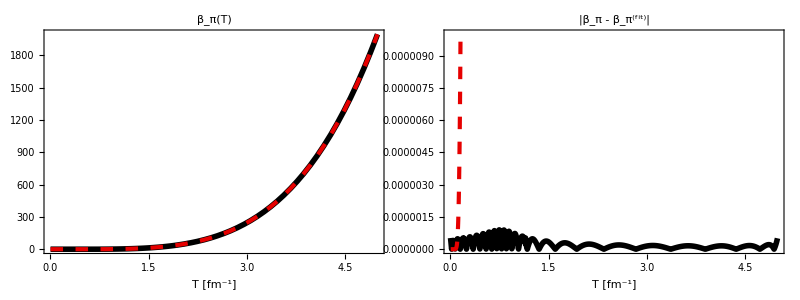

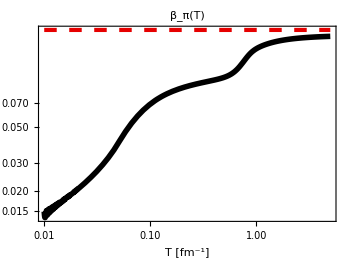

(-2.7066339287950483e-6 + 0.00015147191572394042*T + 0.0025250811767657576*Power(T,2) - 0.19219923978348888*Power(T,3) + 3.5012345849437647*Power(T,4) - 
     34.558566172078464*Power(T,5) + 227.72898723453454*Power(T,6) - 1057.5862752877038*Power(T,7) + 3440.83923021774*Power(T,8) - 7828.311079436474*Power(T,9) + 
     12408.654873466738*Power(T,10) - 13464.524999561829*Power(T,11) + 9558.158920274876*Power(T,12) - 4006.4555725779414*Power(T,13) + 751.6324994786531*Power(T,14)
     )/(4.948544823459247 - 49.08511984532813*T + 190.300710355771*Power(T,2) - 490.72536553131215*Power(T,3) + 1100.3638519481958*Power(T,4) - 
     2171.919687140666*Power(T,5) + 3341.606064835708*Power(T,6) - 3657.513530455562*Power(T,7) + 2660.0122931825754*Power(T,8) - 1156.9633916662917*Power(T,9) + 
     229.42907680310904*Power(T,10) - 1.2735787014866995*Power(T,11) + 0.13180043195835162*Power(T,12) - 0.008175916504696873*Power(T,13) + 
     0.00022965987058812013*Power(T,14))

```mathematica
betapiconformal[T_]=0.2*(edInt[T]+PInt[T]);

Grid[{{Plot[{betapi[T],betapifit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betapi[T]-betapifit[T]],betapi[T]},{T,0.001,5},PlotRange->{0,0.00001},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_π - β_π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

LogLogPlot[{betapi[T]/(edInt[T]+PInt[T]),betapiconformal[T]/(edInt[T]+PInt[T])},{T,0.01,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]



betapifit[T]//CForm
```

```mathematica
betaPiDataRaw=Import[wd<>"/betabulkplot.dat"];
betaPiData= Take[betaPiDataRaw,{3,Length[betaPiDataRaw]}];
betaPi = Interpolation[betaPiData[[All,{1,2}]]];

betaPiconformal[T_]=14.55*(1.0/3.0-cs2Int[T])^2*(edInt[T]+PInt[T]);

(*betaPiconformal[T_]=15*(1.0/3.0-cs2quasi[edInt[T]])^2*(edInt[T]+PInt[T]);*)
n = 14;
betaPifit[T_]=rationalPolyFit[betaPiData,n,n]/.{x->T};
```

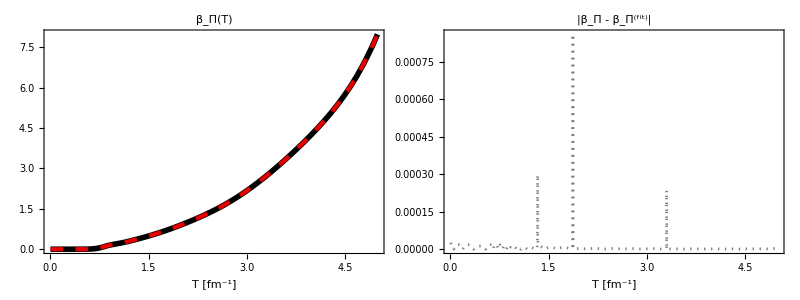

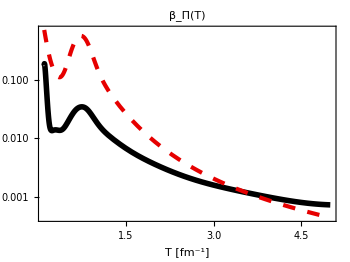

(0.057187918268175174 - 2.5795110808844144*T + 31.966143337661794*Power(T,2) - 186.97202223464143*Power(T,3) + 632.9739160169219*Power(T,4) - 
     1356.8644912535221*Power(T,5) + 1937.6556428262882*Power(T,6) - 1901.4144609887912*Power(T,7) + 1305.7115016142484*Power(T,8) - 632.7107309491553*Power(T,9) + 
     215.7883928137199*Power(T,10) - 50.783337922429304*Power(T,11) + 7.882963305898372*Power(T,12) - 0.7302386364254765*Power(T,13) + 
     0.031006456705249083*Power(T,14))/
   (2168.5818494848654 - 17367.372494454743*T + 62866.89323544513*Power(T,2) - 136008.52657020878*Power(T,3) + 196076.0893015133*Power(T,4) - 
     198954.9682758633*Power(T,5) + 146384.87731197142*Power(T,6) - 79310.95783243925*Power(T,7) + 31803.091369445476*Power(T,8) - 9398.242646642117*Power(T,9) + 
     2016.6245278736917*Power(T,10) - 304.98512854363526*Power(T,11) + 30.758339605713708*Power(T,12) - 1.852389925261096*Power(T,13) + 
     0.05027444936020055*Power(T,14))

```mathematica
Grid[{{Plot[{betaPi[T],betaPifit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_Π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betaPi[T]-betaPifit[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_Π - β_Π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

LogPlot[{betaPi[T]/(edInt[T]+PInt[T]),betaPiconformal[T]/(edInt[T]+PInt[T])},{T,0.1,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_Π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]

betaPifit[T]//CForm
```